### 1d. Green’s Function Plots

-Graphics3D-

t=0

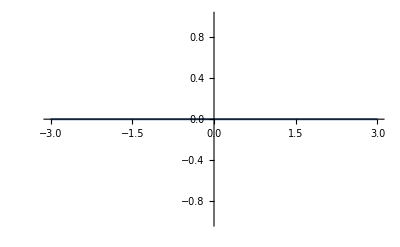

t=0.0001

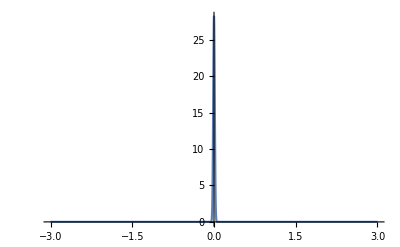

t=1

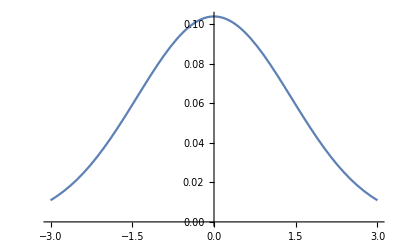

t=10

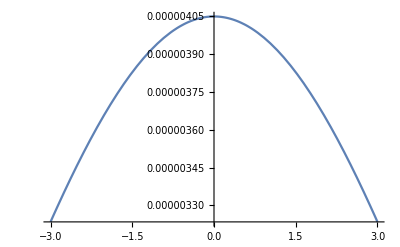

t=100

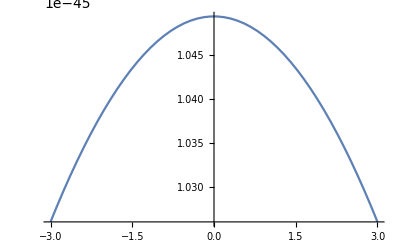

time lapse: t = 0.0001, 0.001, 0.01

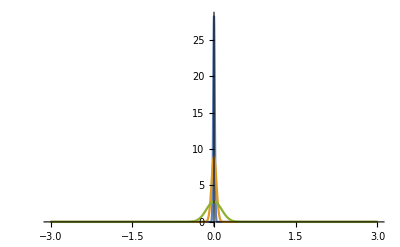

x=0

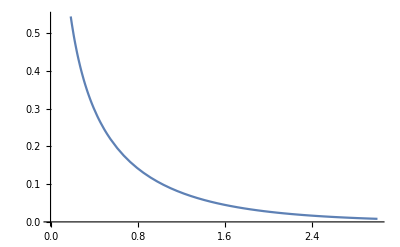

x=2

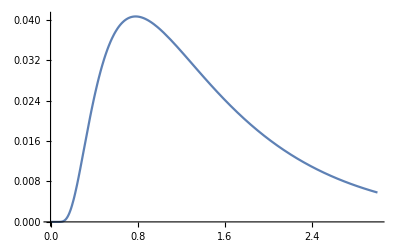

total voltage

ConditionalExpression[ⅇ^-t HeavisideTheta[t],Re[t]>0]

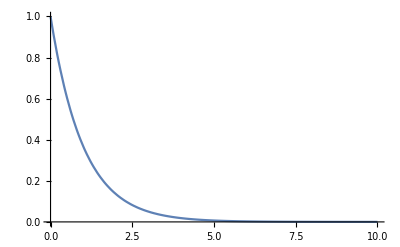

```mathematica
G[x_,t_] = (4*Pi*t)^(-1/2)*Exp[-t-x^2/4/t]*HeavisideTheta[t];
Plot3D[G[x,t],{x,-3,3},{t,0,3}, PlotRange->All, ColorFunction->"TemperatureMap", AxesLabel->Automatic]

(* t=0 *)
Print["t=0"]
Plot[Limit[G[x,t], t->0],{x,-3,3}, AxesLabel->Automatic]

(* t=0.0001 *)
Print["t=0.0001"]
Plot[G[x,0.0001],{x,-3,3}, AxesLabel->Automatic]

(* t=1 *)
Print["t=1"]
Plot[G[x,1],{x,-3,3}, AxesLabel->Automatic]

(* t=10 *)
Print["t=10"]
Plot[G[x,10],{x,-3,3}, AxesLabel->Automatic]

(* t=100 *)
Print["t=100"]
Plot[G[x,100],{x,-3,3}, AxesLabel->Automatic]

(* time lapse: t = 0.0001, 0.001, 0.01 *)
Print["time lapse: t = 0.0001, 0.001, 0.01"]
Plot[{G[x,0.0001], G[x,0.001], G[x,0.01]},{x,-3,3}, PlotRange->All, AxesLabel->Automatic]

(* x=0 *)
Print["x=0"]
Plot[G[0,t],{t,0,3}, AxesLabel->Automatic]

(* x=2 *)
Print["x=2"]
Plot[G[2,t],{t,0,3}, AxesLabel->Automatic]

(* total voltage *)
Print["total voltage"]
Gavg = Integrate[G[x,t],{x,-Infinity, Infinity}]
Plot[Gavg,{t,0,10}, PlotRange->All, AxesLabel->Automatic]
```

### 1e. Plots of Arbitrary Spatiotemporal Inputs Using Fundamental Solution

```mathematica
g[x_,xbar_,t_,tbar_] = (4*Pi*(t-tbar))^(-1/2)*Exp[-(t-tbar)-(x-xbar)^2/4/(t-tbar)]*HeavisideTheta[t-tbar];

(* Jext=(δ(x-1)+δ(x+1))δ(t) *)
Print["Jext=(δ(x-1)+δ(x+1))δ(t)"]
J1[x_,t_] = Integrate[(DiracDelta[xbar-1]+DiracDelta[xbar+1])*DiracDelta[tbar]*g[x,xbar,t,tbar],{xbar,-Infinity,Infinity},{tbar,-Infinity, Infinity}]
Plot3D[J1[x,t],{x,-3,3},{t,0,3}, PlotRange->All]

(* Jext=1 *)
Print["Jext=1"]
J2[x_,t_] = Integrate[G[x-xbar,t-tbar],{xbar,-Infinity,Infinity},{tbar,-Infinity, Infinity}, Assumptions->t∈Reals && x∈Reals && tbar∈Reals && xbar∈Reals]
Plot3D[J2[x,t],{x,-3,3},{t,0,3}, PlotRange->All]


(* Jext=sin(x) *)
Print["Jext=sin(x)"]
J3[x_,t_] = Integrate[Sin[xbar]*g[x,xbar,t,tbar],{xbar,-Infinity,Infinity},{tbar,-Infinity, Infinity}, Assumptions->t∈Reals && x∈Reals && tbar∈Reals && xbar∈Reals]
Plot3D[J3[x,t],{x,-3,3},{t,0,3}, PlotRange->All]
```

Jext=(δ(x-1)+δ(x+1))δ(t)

(ⅇ^(-t-(1+x)^2/(4 t)) (1+ⅇ^(x/t)) UnitStep[t])/(2 √π √t)

-Graphics3D-

Jext=1

1

-Graphics3D-

Jext=sin(x)

1/2 (-(Piecewise[{{-ⅇ^-x/2, x>0}, {-ⅇ^x/2, True}}])+(Piecewise[{{-ⅇ^-x/2, x≥0}, {-ⅇ^x/2, True}}]))

-Graphics3D-